## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Column@Table[ToString@i<>".  ",{i,21}];
```

```mathematica
niceForm[{x_,y_}]:=TraditionalForm[x î + y ĵ]
niceForm[{x_,y_,z_}] := TraditionalForm[x î + y ĵ+z k̂]
```

```mathematica
ihat:={0,1}; ihat3:={1,0,0};
jhat:={1,0}; jhat3:={0,1,0};
khat3:={0,0,1};
```

## 3

```mathematica
reg = ImplicitRegion[0<y<9-x^2,{x,y}];
Integrate[y{x,y,1},{x,y}∈reg] /. {x_,y_,t_}->{t,{x/t,y/t}}
niceForm[%[[2]]]
```

{648/5,{0,36/7}}

(36 ĵ)/7

```mathematica
reg = ImplicitRegion[x>0&&y>0&&z>0&&x+y+z<1,{x,y,z}];
Integrate[y{x,y,z,1},{x,y,z}∈reg] /. {x_,y_,z_,t_}->{t,{x/t,y/t,z/t}}
niceForm[%[[2]]]
```

{1/24,{1/5,2/5,1/5}}

(î)/5+(2 ĵ)/5+(k̂)/5

## 4

```mathematica
block1=ImplicitRegion[-2<x<10&&0<y<6&&0<z<10,{x,y,z}]
block2=TransformedRegion[ImplicitRegion[3<x<6&&0<y<3&&10<z<13,{x,y,z}],
RotationTransform[Pi/4,{0,1,1}]]
cyl1=TransformedRegion[ImplicitRegion[0<x^2+y^2<4&&-3<z<10,{x,y,z}],RotationTransform[-Pi/3,{1,0,0}]]
```

ImplicitRegion[-2<x<10&&0<y<6&&0<z<10,{x,y,z}]

ParametricRegion[{{x/(√2)-y/2+z/2,x/2+1/4 (2+√2) y+1/4 (2-√2) z,-x/2+1/4 (2-√2) y+1/4 (2+√2) z},3<x<6&&0<y<3&&10<z<13},{x,y,z}]

ParametricRegion[{{x,y/2+(√3 z)/2,-(√3 y)/2+z/2},0<x^2+y^2<4&&-3<z<10},{x,y,z}]

```mathematica
Show[Table[RegionPlot3D[i,PlotPoints->30,PlotStyle->Directive[Opacity[0.5]]],{i,{block1,block2,cyl1}}]]
```

-Graphics3D-

Regions1.png

```mathematica
combinedRegion = RegionDifference[RegionUnion[block1,block2],cyl1];
RegionPlot3D[combinedRegion,PlotPoints->100,PlotStyle->Directive[Opacity[0.5]]]
```

-Graphics3D-

```mathematica
(*Export["Regions2.png",Rasterize[%,RasterSize->400]]*)
```

Regions2.png

```mathematica
RegionMeasure[combinedRegion]
```

-((128 (-1685134704180765409782653450925-1191570176539005978374428972500 √2-16508296568530178043890226304 √3-11673128449446301954906353280 √6+37143667279192900598753009184 √3 π+26264539011254179398539294880 √6 π))/(9 (-2+√2)^2 (1+√2)^6 (2+√2)^4 (3+2 √2)^5 (4+3 √2)^5 (10+7 √2)^2 (17+12 √2)^5 (58+41 √2)^3))

```mathematica
N[RegionMeasure[combinedRegion]]
```

651.143

## 4 (comp)

```mathematica
L[x_]:=200 Sqrt[1-x^2/17]
FunctionDomain[L[x],x]
Integrate[L[x]{x,1},{x,0,Sqrt[17]}] /. {x_,t_}->{t,{x/t}}
```

-√17≤x≤√17

{50 √17 π,{(4 √17)/(3 π)}}

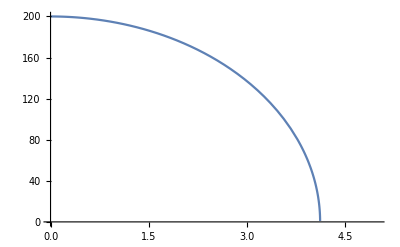

```mathematica
Plot[L[x],{x,0,5}]
```

## 5

```mathematica
innerShell=Cylinder[{{1,0,0},{199,0,0}},15/2];
outerShell = Cylinder[{{0,0,0},{200,0,0}},17/2];
tube = (*Note: Units are cm *) RegionDifference[outerShell,innerShell];
```

```mathematica
RegionPlot3D[tube,PlotStyle->Directive[Opacity[0.5]],PlotPoints->40]
```

-Graphics3D-

```mathematica
tubeMass = Quantity[1, ("Centimeters")^3]*RegionMeasure[tube]*Entity["Element","Aluminum"][EntityProperty["Element","Density"]]
```

28000. g

```mathematica
tubeBuoyancy= Quantity[1, ("Centimeters")^3]*RegionMeasure[outerShell]*Entity["Chemical","Water"][EntityProperty["Chemical","Density"]]
```

45396. g

```mathematica
UnitConvert@tubeBuoyancy*2
UnitConvert@tubeMass*3
```

90.792 kg

84. kg

```mathematica
Module[{waterHeight,reg},
underwaterRegion[region_,waterLevel_]:=RegionIntersection[region,HalfSpace[{0,0,1},waterLevel]];
(* underwaterVolume[region] computes and caches a symbolic expression for the amount of volume underwater in terms of waterHeight *)
underwaterVolume[region_]:=underwaterVolume[region]=(
reg:=underwaterRegion[region,waterHeight];
RegionMeasure[reg]
);
underwaterVolume[region_,waterLevel_]:=underwaterVolume[region]/.waterHeight->waterLevel
]
```

```mathematica
N@underwaterVolume[outerShell,∞]
```

45396.

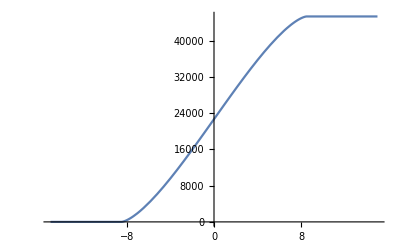

```mathematica
Plot[underwaterVolume[outerShell,x],{x,-15,15}]
```

```mathematica
neededVolume=QuantityMagnitude@UnitConvert[tubeMass*3/2/Entity["Chemical","Water"][EntityProperty["Chemical","Density"]],"cm^3"]
```

42146.4

```mathematica
waterLevel=(x/.Solve[underwaterVolume[outerShell,x]==neededVolume,x,Reals])[[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

6.38639

```mathematica
QuantityMagnitude@UnitConvert[tubeMass*3/2]
```

42.

```mathematica
buoyancy[3]
```

buoyancy[3]

```mathematica
niceForm@RegionCentroid[underwaterRegion[outerShell,waterLevel]]
```

100. î-0.55834 k̂+0.

```mathematica
RegionPlot3D[underwaterRegion[outerShell,waterLevel],PlotPoints->50]
Show[RegionPlot3D[outerShell],Plot3D[waterLevel,{x,-10,210},{y,-10,10},ColorFunction->"BlueGreenYellow"]]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Export["cyl1.png",Out[417]]*)
```

cyl1.png

```mathematica
UnitConvert[3*(tubeBuoyancy-tubeMass)]
```

51.8952 kg

## 6

```mathematica
cyl1=Cylinder[{{-50,0,0},{50,0,0}},15];
sphere1=Ball[{-50,0,0},15];
sphere2=Ball[{50,0,0},15];
chop = ImplicitRegion[z<0,{x,y,z}];
reg=RegionIntersection[RegionUnion[sphere1,sphere2,cyl1],chop];
```

```mathematica
RegionPlot3D[RegionMember[reg][{x,y,z}],{x,-80,80},{y,-80,80},{z,-80,80},PlotPoints->60]
```

-Graphics3D-

```mathematica
RegionMeasure[reg]
```

13500 π

```mathematica
RegionCentroid[reg]
```

{0,0,-(5 (160+9 π))/(48 π)}

### Thin shell

```mathematica
r=15;
cyl1=ImplicitRegion[y^2+z^2==r^2&& z<0&&-50<x<50,{x,y,z}];
sphere1=RegionIntersection[Sphere[{50,0,0},15],ImplicitRegion[x>50&&z<0,{x,y,z}]];
sphere2=RegionIntersection[Sphere[{-50,0,0},15],ImplicitRegion[x<-50&&z<0,{x,y,z}]];
chop = ImplicitRegion[-50-Sqrt[r^2-y^2]<x<Sqrt[r^2-y^2]+50&&z==0,{x,y,z}];
regs={sphere1,sphere2,cyl1,chop};
regShell=RegionUnion[sphere1,sphere2,cyl1,chop];
```

```mathematica
RegionMeasure@regShell
```

75 (40+29 π)

WolframAlphaQueryResults

7.859 g/cm^3

```mathematica
mass=UnitConvert[RegionMeasure@regShell Quantity[, ("Centimeters")^2]*Quantity[0.1, "Centimeters"]*Quantity[7.859, ("Grams")/("Centimeters")^3]]
masswater=UnitConvert[RegionMeasure@reg Quantity[, ("Centimeters")^3]*Entity["Chemical","Water"][EntityProperty["Chemical","Density"]]]
```

7.72773 kg

42.4115 kg

```mathematica
Map[DiscretizeRegion,regShell]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Export["regs.png",Rasterize[{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},RasterSize->1500]]
```

regs.png

```mathematica
Show[Map[DiscretizeRegion,regShell],Boxed->True]
```

-Graphics3D-

```mathematica
niceForm@N@RegionCentroid[regShell]
```

0.-5.65474 k̂

```mathematica
-(15 (40+3 π) k̂)/(40+29 π)
```

```mathematica
COB=Integrate[{x,y,z,1},{x,y,z}∈regShell] /. {x_,y_,z_,t_}->{t,{x/t,y/t,z/t}}
```

{75 (40+29 π),{0,0,-(15 (40+3 π))/(40+29 π)}}

### Floating height

This is being stupid, so I switched to meters instead of cm.

```mathematica
capsule=CapsuleShape[{{-50,0,0},{50,0,0}}/100,15./100];
chop =HalfSpace[{0,0,1},0];
reg=RegionIntersection[capsule,chop];
```

```mathematica
Module[{waterHeight,reg},
underwaterVolumeNocache[region_, waterLevel_]:=(
reg:=RegionIntersection[region,HalfSpace[{0,0,1},waterLevel]];
If[RegionDistance[reg,{0,0,0}]==∞,0,
Volume[DiscretizeRegion@reg]]
)
]
```

```mathematica
Dynamic[reg]
```

```mathematica
underwaterVolumeNocache[reg,1]
```

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region RegionIntersection[«2»].

Volume::reg: DiscretizeRegion[RegionIntersection[HalfSpace[{0,0,1},1],RegionIntersection[CapsuleShape[{{-1/2,0,0},{1/2,0,0}},0.15],HalfSpace[{0,0,1},0]]]] is not a correctly specified region.

Volume[DiscretizeRegion[RegionIntersection[HalfSpace[{0,0,1},1],RegionIntersection[CapsuleShape[{{-1/2,0,0},{1/2,0,0}},0.15],HalfSpace[{0,0,1},0]]]]]

```mathematica
Plot[underwaterVolumeNocache[reg,x],{x,-.2,0},PlotPoints->10]
```

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region RegionIntersection[«2»].

Volume::reg: DiscretizeRegion[RegionIntersection[HalfSpace[{0,0,1},-0.199978],RegionIntersection[CapsuleShape[{{-1/2,0,0},{1/2,0,0}},3/20],HalfSpace[{0,0,1},0]]]] is not a correctly specified region.

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region RegionIntersection[«2»].

Volume::reg: DiscretizeRegion[RegionIntersection[HalfSpace[{0.,0.,1.},-0.199978],RegionIntersection[CapsuleShape[{{-0.5,0.,0.},{0.5,0.,0.}},0.15],HalfSpace[{0.,0.,1.},0.]]]] is not a correctly specified region.

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region RegionIntersection[«2»].

General::stop: Further output of DiscretizeRegion::drf will be suppressed during this calculation.

Volume::reg: DiscretizeRegion[RegionIntersection[HalfSpace[{0,0,1},-0.177756],RegionIntersection[CapsuleShape[{{-1/2,0,0},{1/2,0,0}},3/20],HalfSpace[{0,0,1},0]]]] is not a correctly specified region.

General::stop: Further output of Volume::reg will be suppressed during this calculation.

$Aborted

```mathematica
RegionMeasure@capsule
```

(27 π)/1000

```mathematica
DiscretizeRegion[reg]
```

-Graphics3D-

```mathematica
N@RegionMeasure@reg
```

42411.5

```mathematica
underwaterVolume[reg]
```

$Aborted

```mathematica
Volume[reg]
```

$Aborted

```mathematica
Volume@DiscretizeRegion@reg
```

0.0414276

```mathematica
DiscretizeRegion[RegionIntersection[HalfSpace[{0,0,1},100],CapsuleShape[{{-1/2,0,0},{1/2,0,0}},0.15],HalfSpace[{0,0,1},0]]]
```

-Graphics3D-

```mathematica
underwaterVolumeNocache[reg,100]
```

Volume::reg: DiscretizeRegion[RegionIntersection[HalfSpace[{0,0,1},100],RegionIntersection[CapsuleShape[{{-1/2,0,0},{1/2,0,0}},0.15],HalfSpace[{0,0,1},0]]]] is not a correctly specified region.

Volume[DiscretizeRegion[RegionIntersection[HalfSpace[{0,0,1},100],RegionIntersection[CapsuleShape[{{-1/2,0,0},{1/2,0,0}},0.15],HalfSpace[{0,0,1},0]]]]]